```mathematica
Remove["Global`*"]
```

# Poincare Maps

```mathematica
eq1[μ_]:={ v'[t] ==( r[t] ω[t]^2 + 9.8 (Cos[θ[t]] -μ ))/(1+μ), ω'[t] ==(- 2v[t] ω[t] - 9.8 Sin[θ[t]])/r[t],r'[t] == v[t],θ'[t] ==ω[t]};
```

```mathematica
psect[{r0_, θ0_, v0_, ω0_}]:=Reap[NDSolve[{eq1[3],r[0]==r0,θ[0]==θ0,v[0] == v0, ω[0] == ω0,WhenEvent[θ[t]==0,Sow[{r[t],v[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]
```

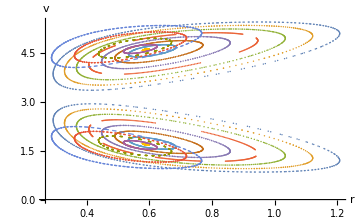

```mathematica
abcdata=Mod[Map[psect,{{1,Pi/2,0,0}, {1,Pi/2-0.1, 0, 0},{1,Pi/2-0.2, 0, 0},{1,Pi/2-0.3, 0, 0},{1,Pi/2-0.4, 0, 0},{1,Pi/2-0.5, 0, 0},{1,Pi/2-0.6, 0, 0},{1,Pi/2-0.7, 0, 0},{1,Pi/2-0.8, 0, 0},{1,Pi/2-0.9, 0, 0},{1,Pi/2-1, 0, 0},{1,Pi/2-1.1, 0, 0} }],2 π];
ListPlot[abcdata,ImageSize->Medium, AxesLabel->{r,v}]
```

Above is the Poincare map (r vs v) for the system, varying the initial angle θ(0)

```mathematica
Export["/home/hp/Desktop/acads/SAM/poincare_r.jpg",%201,"JPEG"]
```

/home/hp/Desktop/acads/SAM/poincare_r.jpg

```mathematica
psect[{r0_, θ0_, v0_, ω0_}]:=Reap[NDSolve[{eq1[8],r[0]==r0,θ[0]==θ0,v[0] == v0, ω[0] == ω0,WhenEvent[θ[t]==0,Sow[{r[t],v[t]}]]},{},{t,0,1000},MaxSteps->∞]][[-1,1]]
dat = Mod[Map[psect,{{1,Pi/2,0,0}}],2Pi];
p7= ListPlot[dat, PlotRange->{{0,1.3},{0,6}},PlotLabel->{r(t), v(t)}]
```

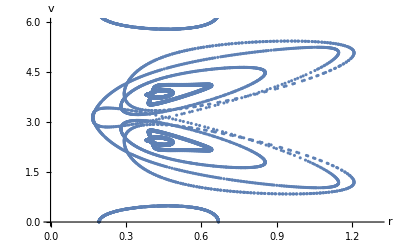

```mathematica
Show[p1,p2,p3,p4,p5,p6,p7,AxesLabel->{r, v}]
```

This is the Poincare map (r vs v) for the system, varying the initial angle θ (0)

```mathematica
Export["/home/hp/Desktop/acads/SAM/poincare_mu.jpg",%189,"JPEG"]
```

/home/hp/Desktop/acads/SAM/poincare_mu.jpg

# Phase Space Plots

```mathematica
μ = 3;
sol1 =NDSolve[{ v'[t] ==( r[t] ω[t]^2 + 9.8 (Cos[θ[t]] - μ))/(1+μ), ω'[t] ==(- 2v[t] ω[t] - 9.8 Sin[θ[t]])/r[t],r'[t] == v[t],θ'[t] ==ω[t], r[0]==1, θ[0] == Pi/2,v[0] == 0, ω[0] == 0}, {r,v, θ, ω},{t, 0, 100}, MaxSteps->200000]
```

{{r→InterpolatingFunction[…],v→InterpolatingFunction[…],θ→InterpolatingFunction[…],ω→InterpolatingFunction[…]}}

### r vs v:

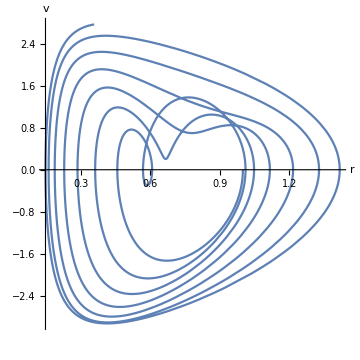

```mathematica
a[t_]:=r[t]/.sol1
b[t_]:=v[t]/.sol1

ParametricPlot[{a[t][[1]],b[t][[1]]},{t,0,10}, AspectRatio->1, ImageSize->Medium, AxesLabel->{r,v}]
```

### θ vs ω:

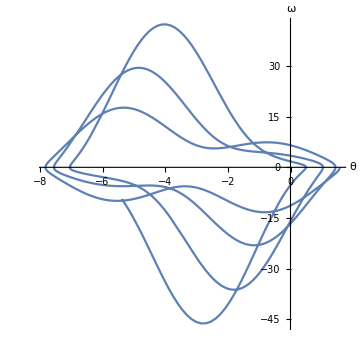

```mathematica
c[t_]:=θ[t]/.sol1
d[t_]:=ω[t]/.sol1
ParametricPlot[{c[t][[1]],d[t][[1]]},{t,0,10}, AspectRatio->1, ImageSize->Medium, AxesLabel->{θ, ω}, PlotRange->Full]
```